Calculation of the target precision ϵ for the control precision δ and the leakage to non-qubit levels r , Eq. 81

```mathematica
s=1.5;
ep=0.1;
n=40;
c=3.5;
op=2;
```

We start with the simplified expressions:

```mathematica
rb =16 ep s /(2 c(2+s));
N[rb]
```

0.0979592

thus the value taken from experimental papers r=0.1 is in r>rb range. We compute the reduction factor α_c

```mathematica
r=0.1;
del=0.0001;
mE = ep s op/2;
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
ac = (mE -A2)/(2 A1)
```

0.000387318

Finally we check the inequality

```mathematica
del r
8 (ep s)^2 op/(2c* 81* n (2+s)^3)
```

0.00001

3.70216×10^-7

It is not satisfied. Let us compute the δ that is required

```mathematica
8 (ep s)^2 op/(2c*r* 81* n (2+s)^3)
```

3.70216×10^-6

Let us also compute α_b

```mathematica
del=0.0001;
ab=(op/(16 n (s+2))-del)/2
```

0.000396429

and δ_b

```mathematica
delb = mE/(81 n (2+s)^2)
```

3.77929×10^-6

so our scaling estimates, when used directly, suggest that six digits of precision is required. Let us instead us a more accurate inequality:

```mathematica
2 mE
```

0.3

```mathematica
del=1.6*10^(-5);
c r n (2+s)^2 del +2 Sqrt[c r (1+r) n (2+s)^3del op]
```

0.293459

using the exact expression wins one order of magnitude. Let us now investigate  larger plasma frequencies

```mathematica
n=40
op=10
r=0.1;
del=0.004;
mE = ep s op/2;
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
ac = (mE -A2)/(2 A1)
```

40

10

0.000186589

we check the inequality

```mathematica
del r
8 (ep s)^2 op/(2c* 81* n (2+s)^3)
```

0.0004

1.85108×10^-6

It is not satisfied. Let us compute the δ that is required

```mathematica
8 (ep s)^2 op/(2c*r* 81* n (2+s)^3)
```

0.0000185108

that’s five digits of precision. The more accurate inequality gives:

```mathematica
2 mE
```

1.5

```mathematica
del=8*10^(-5);
c r n (2+s)^2 del +2 Sqrt[c r (1+r) n (2+s)^3del op]
```

1.46729

using the exact expression wins one order of magnitude. Let us now investigate smaller systems and larger plasma frequencies

```mathematica
n=4
op=10
r=0.1;
del=0.01;
mE = ep s op/2;
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
ac = (mE -A2)/(2 A1)
```

4

10

0.0168659

we check the inequality

```mathematica
del r
8 (ep s)^2 op/(2c* 81* n (2+s)^3)
```

0.001

0.0000185108

It is not satisfied. Let us compute the δ that is required

```mathematica
8 (ep s)^2 op/(2c*r* 81* n (2+s)^3)
```

0.000185108

that’s four digits of precision. The more accurate inequality gives:

```mathematica
2 mE
```

1.5

```mathematica
del=8.3*10^(-4);
c r n (2+s)^2 del +2 Sqrt[c r (1+r) n (2+s)^3del op]
```

1.49481

that’s three to four digits of precision needed for the all-to-all (2s=3) 4 qubit system

using the α_b instead of α_c

```mathematica
del=0.00067;
ep=0.1;
r=0.1;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

0.0219864

-0.000157609

Finally let’s find out which ϵ can be obtained with the precision of the flux qubits reported in the literature

```mathematica
ep=0.5;
n=4;
op=10;
r=0.1;
del=0.01;
mE = ep s op/2;
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
```

```mathematica
rb =16 ep s /(2 c(2+s));
N[rb]
```

0.489796

we will need α_b

```mathematica
del=0.01;
ab=(op/(16 n (s+2))-del)/2
```

0.0173214

and δ_b

```mathematica
delb = mE/(81 n (2+s)^2)
```

0.000944822

only 3 digits of precision, but not two. We would like to work with the starting inequality directly using α_b

```mathematica
del=0.01;
ep=1.4;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

0.0173214

-0.00511927

Only at ϵ=1.4 is the inequality satisfied. Reducing r doesn’t change much:

```mathematica
del=0.01;
ep=1.4;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

smaller plasma frequencies work much worse

```mathematica
op=2;
del=0.005;
ep=6;
r=0.01;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

0.00196429

-0.000333616

n -dependence of ϵ

using the α_b instead of α_c

```mathematica
n=30;
op=10;
del=0.0001;
ep=0.11;
r=0.1;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

0.00292619

-0.0000790766

```mathematica
n=52;
op=10;
del=0.0001;
ep=0.17;
r=0.1;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

0.00166703

-0.000032232

```mathematica
n=70;
op=10;
del=0.0001;
ep=0.22;
r=0.1;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

0.00122551

-0.0000115777

```mathematica
n=100;
op=10;
del=0.0001;
ep=0.31;
r=0.1;
ab=(op/(16 n (s+2))-del)/2
A1=c r n(2+s)^2;
A2=c r n(2+s)^2del;
A3=del(2+s)op;
(1+r)A1 ab^2 +(A2 -ep s op)ab +A3
```

0.000842857

-0.000048102

predicted values from δ_b are much bigger

```mathematica
2 del (81 n (2+s)^2)/(s op)
```

1.323

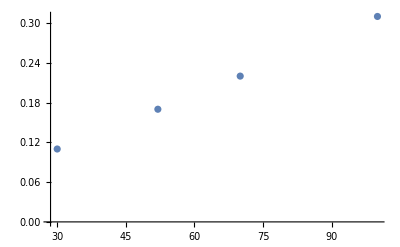

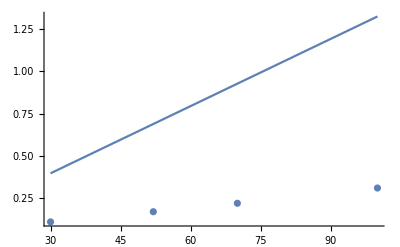

```mathematica
p1 =Plot[2 del (81 np (2+s)^2)/(s op),{np,30,100}];
p2= ListPlot[{{30,0.11},{52,0.17},{70,0.22},{100,0.31}}]
Show[p2,p1,PlotRange->All]
```

both of them appear to be linear